# Half step method for y’=x+y

```mathematica
data={{0,1}}; (*setting up a dataset to which the Do loop data will be sent to. includes initial condition y(0)=1*)
h=0.1; (*step size*)
y0=1;(*initial condition that will be used in the Do loop*)
```

```mathematica
Do[y1=y0+((x-0.05)+(y0+((x-0.1)+y0)*h/2))*h; AppendTo[data,{x,y1}]; y0=y1, {x,0.1,10,h}] (*calculating y(x+h)=y(x)+y'(x+h/2)*h with y'(x)=x+y and h=0.1 from x=0.1 to x=10 (x=0 is already included in the data set). for each iteration the (x+h, y(x+h)) data is stored in the set "data" defined earlier.*)
```

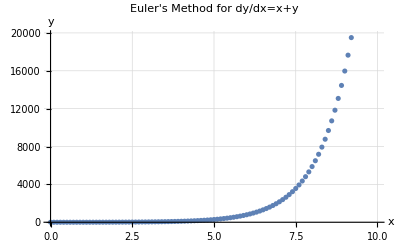

```mathematica
ListPlot[data,PlotLabel->"Euler's Method for dy/dx=x+y",GridLines->Automatic,AxesLabel->{"x","y"}](*plotting the data in the set "data", labeling the plot, setting up gridlines, and labeling the axes.*)
```

# Half step method for y' =ylny/x, N=10

```mathematica
data1={{2,Exp[1]}}; 
h2=0.2;
y2=Exp[1];
```

```mathematica
Do[y1=y2+(y2+y2*Log[y2]*h2/((x-h2)*2)*Log[y2+y2*Log[y2]*h2/((x-h2)*2)])*h2/(x-h2/2); AppendTo[data1,{x,y1}]; y2=y1, {x,2.2,4,h2}]
```

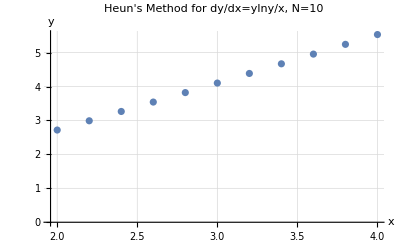

```mathematica
ListPlot[data1,PlotLabel->"Heun's Method for dy/dx=ylny/x, N=10",GridLines->Automatic,AxesLabel->{"x","y"}]
```

```mathematica
solution=data1
```

{{2,ⅇ},{2.2,2.99074},{2.4,3.26562},{2.6,3.54274},{2.8,3.82192},{3.,4.10301},{3.2,4.38588},{3.4,4.6704},{3.6,4.95646},{3.8,5.24397},{4.,5.53282}}

# Half step method for y' = ylny/x, N = 1000

```mathematica
data2={{2,Exp[1]}}; 
h3=0.002;
y2=Exp[1];
```

```mathematica
Do[y1=y2+(y2+y2*Log[y2]*h3/((x-h3)*2)*Log[y2+y2*Log[y2]*h3/((x-h3)*2)])*h3/(x-h3/2); AppendTo[data2,{x,y1}]; y2=y1, {x,2.002,4,h3}]
```

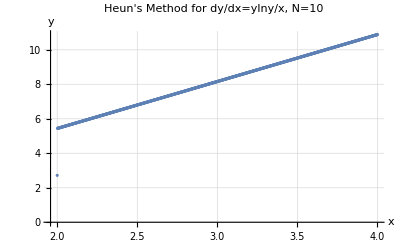

```mathematica
ListPlot[data2,PlotLabel->"Heun's Method for dy/dx=ylny/x, N=10",GridLines->Automatic,AxesLabel->{"x","y"}]
```

# Heun' s method for y' = (x^2 + y^2 + 1)^1/3, N = 10

```mathematica
data3={{0,0}}; 
h4=0.5;
y3=0;
```

```mathematica
Do[y1=y3+((x-h4/2)^2+(y3+((x-h4)^2+y3^2+1)^(1/3)*h4/2)^2+1)^(1/3)*h4; AppendTo[data3,{x,y1}]; y3=y1, {x,0.5,5,h4}]
```

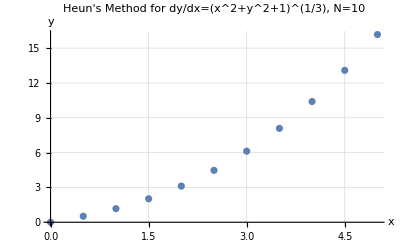

```mathematica
ListPlot[data3,PlotLabel->"Heun's Method for dy/dx=(x^2+y^2+1)^(1/3), N=10",GridLines->Automatic,AxesLabel->{"x","y"}]
```

```mathematica
solution2=data3
```

{{0,0},{0.5,0.520021},{1.,1.17175},{1.5,2.02414},{2.,3.11425},{2.5,4.47034},{3.,6.11881},{3.5,8.08595},{4.,10.3983},{4.5,13.0827},{5.,16.1663}}

# Heun' s method for y' = (x^2 + y^2 + 1)^1/3, N = 10

```mathematica
data4={{0,0}}; 
h5=0.005;
y3=0;
```

```mathematica
Do[y1=y3+((x-h5/2)^2+(y3+((x-h5)^2+y3^2+1)^(1/3)*h5/2)^2+1)^(1/3)*h5; AppendTo[data4,{x,y1}]; y3=y1, {x,0.005,5,h5}]
```

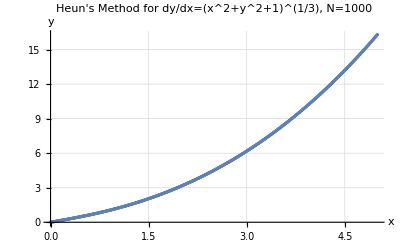

```mathematica
ListPlot[data4,PlotLabel->"Heun's Method for dy/dx=(x^2+y^2+1)^(1/3), N=1000",GridLines->Automatic,AxesLabel->{"x","y"}]
```